```mathematica
L = [{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883}, {512,0.047099},{1024,0.029178}]
```

```mathematica
L
```

L

```mathematica
L[0]
```

L[0]

```mathematica
a =
```

{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}}

```mathematica
a
```

a

```mathematica
ListPlot[{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883}, {512,0.047099},{1024,0.029178}]
```

ListPlot::nonopt: Options expected (instead of {1024,0.029178}) beyond position 1 in ListPlot[{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}]. An option must be a rule or a list of rules.

ListPlot[{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}]

```mathematica
L =  {{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883}, {512,0.047099},{1024,0.029178}}
```

{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}}

```mathematica
SortBy[L,First]
```

{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}}

```mathematica
L
```

{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}}

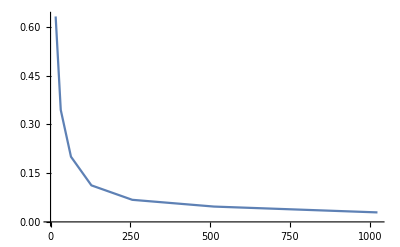

```mathematica
ListLinePlot[L]
```

```mathematica
data = L
```

{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}}

```mathematica
NonlinearModelFit[L]
```

NonlinearModelFit::argr: NonlinearModelFit called with 1 argument; 4 arguments are expected.

NonlinearModelFit[{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}}]

```mathematica
NonlinearModelFit[data, -Log[a+bx]+c,{a,b,c},x]
```

NonlinearModelFit::fdss: Search specification {{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}} should be a list with 1 to 5 elements.

NonlinearModelFit[{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}},{{c-Log[16+bx],c-Log[0.631512+bx]},{c-Log[32+bx],c-Log[0.344124+bx]},{c-Log[64+bx],c-Log[0.200356+bx]},{c-Log[128+bx],c-Log[0.112299+bx]},{c-Log[256+bx],c-Log[0.067883+bx]},{c-Log[512+bx],c-Log[0.047099+bx]},{c-Log[1024+bx],c-Log[0.029178+bx]}},{{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}},b,c},x]

```mathematica
NonlinearModelFit[L, -Log[a+bx]+c,{a,b,c},x]
```

NonlinearModelFit::fdss: Search specification {{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}} should be a list with 1 to 5 elements.

NonlinearModelFit[{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}},{{c-Log[16+bx],c-Log[0.631512+bx]},{c-Log[32+bx],c-Log[0.344124+bx]},{c-Log[64+bx],c-Log[0.200356+bx]},{c-Log[128+bx],c-Log[0.112299+bx]},{c-Log[256+bx],c-Log[0.067883+bx]},{c-Log[512+bx],c-Log[0.047099+bx]},{c-Log[1024+bx],c-Log[0.029178+bx]}},{{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}},b,c},x]

```mathematica
l = {{0,1},{1,5},{0.5,7}}
```

{{0,1},{1,5},{0.5,7}}

```mathematica
NonlinearModelFit[l, -Log[a+bx]+c,{a,b,c},x]
```

NonlinearModelFit::fdss: Search specification {{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}} should be a list with 1 to 5 elements.

NonlinearModelFit[{{0,1},{1,5},{0.5,7}},{{c-Log[16+bx],c-Log[0.631512+bx]},{c-Log[32+bx],c-Log[0.344124+bx]},{c-Log[64+bx],c-Log[0.200356+bx]},{c-Log[128+bx],c-Log[0.112299+bx]},{c-Log[256+bx],c-Log[0.067883+bx]},{c-Log[512+bx],c-Log[0.047099+bx]},{c-Log[1024+bx],c-Log[0.029178+bx]}},{{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}},b,c},x]

```mathematica
NonlinearModelFit[l, {-Log[a+bx]+c},{a,b,c},x]
```

NonlinearModelFit::fdss: Search specification {{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}} should be a list with 1 to 5 elements.

NonlinearModelFit[{{0,1},{1,5},{0.5,7}},{{{c-Log[16+bx],c-Log[0.631512+bx]},{c-Log[32+bx],c-Log[0.344124+bx]},{c-Log[64+bx],c-Log[0.200356+bx]},{c-Log[128+bx],c-Log[0.112299+bx]},{c-Log[256+bx],c-Log[0.067883+bx]},{c-Log[512+bx],c-Log[0.047099+bx]},{c-Log[1024+bx],c-Log[0.029178+bx]}}},{{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}},b,c},x]

```mathematica
l
```

{{0,1},{1,5},{0.5,7}}

```mathematica
nlm=NonlinearModelFit[data,Log[a+b x^2],{a,b},x]
```

NonlinearModelFit::fdss: Search specification {{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}} should be a list with 1 to 5 elements.

NonlinearModelFit[{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}},{{Log[16+b x^2],Log[0.631512+b x^2]},{Log[32+b x^2],Log[0.344124+b x^2]},{Log[64+b x^2],Log[0.200356+b x^2]},{Log[128+b x^2],Log[0.112299+b x^2]},{Log[256+b x^2],Log[0.067883+b x^2]},{Log[512+b x^2],Log[0.047099+b x^2]},{Log[1024+b x^2],Log[0.029178+b x^2]}},{{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}},b},x]

```mathematica
nlm=NonlinearModelFit[l,Log[a+b x^2],{a,b},x]
```

NonlinearModelFit::fdss: Search specification {{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}} should be a list with 1 to 5 elements.

NonlinearModelFit[{{0,1},{1,5},{0.5,7}},{{Log[16+b x^2],Log[0.631512+b x^2]},{Log[32+b x^2],Log[0.344124+b x^2]},{Log[64+b x^2],Log[0.200356+b x^2]},{Log[128+b x^2],Log[0.112299+b x^2]},{Log[256+b x^2],Log[0.067883+b x^2]},{Log[512+b x^2],Log[0.047099+b x^2]},{Log[1024+b x^2],Log[0.029178+b x^2]}},{{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}},b},x]

```mathematica
Clear[a]
```

```mathematica
nlm=NonlinearModelFit[data, -Log[a+bx]+c,{a,b,c},x]
```

NonlinearModelFit::nrlnum: The function value {0.368488-1. Log[1.+bx],0.655876-1. Log[1.+bx],0.799644-1. Log[1.+bx],0.887701-1. Log[1.+bx],0.932117-1. Log[1.+bx],0.952901-1. Log[1.+bx],0.970822-1. Log[1.+bx]} is not a list of real numbers with dimensions {7} at {a,b,c} = {1.,1.,1.}.

NonlinearModelFit[{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}},c-Log[a+bx],{a,b,c},x]

```mathematica
nlm=NonlinearModelFit[data, -Log[a+bx]+c,{a,b,c},{x,y}]
```

NonlinearModelFit::fitc: Number of coordinates (1) is not equal to the number of variables (2).

NonlinearModelFit[{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}},c-Log[a+bx],{a,b,c},{x,y}]

```mathematica
nlm=NonlinearModelFit[data, a^{b+c*Log[x]},{a,b,c},x]
```

FittedModel[6.13146/x^0.822542]

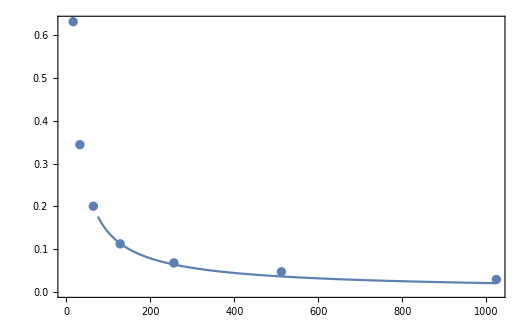

```mathematica
Show[ListPlot[data],Plot[nlm[x],{x,0,1024}],Frame->True]
```

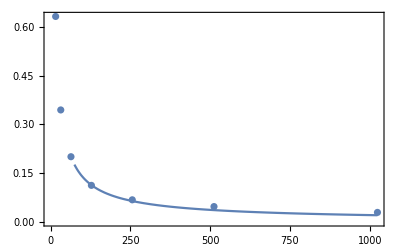

```mathematica
Show[%66,Axes->False]
```

```mathematica
nlm[50]
```

0.245522

```mathematica
nlm
```

FittedModel[Log[1694.04-9.76386 x^2]]

```mathematica
Plot[nlm]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[nlm]

```mathematica
Plot[nlm,{x,0,7}]
```

-Graphics-

```mathematica
nlm[200]
```

-12.9534-3.14159 ⅈ

```mathematica
Plot[1/log(n), {n, 0, 1024}]
```

-Graphics-

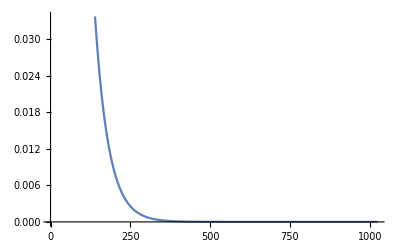

```mathematica
Plot[{nlm[x]}, {x,0,1024}]
```

```mathematica
nlm[x]
```

-Log[-3240.27+302.192 x-11.9866 x^2]

```mathematica
Show[ListPlot[data],Plot[nlm[x],{x,0,1024}],Frame->True]
```

-Graphics-

```mathematica
nlm[16]
```

```mathematica
0.6267940339068501
```

```mathematica
nlm=NonlinearModelFit[data, a^{b+c*Log[x]},{a,b,c},x]
```

FittedModel[6.13146/x^0.822542]

```mathematica
nlm2=NonlinearModelFit[data, {a+b*Log[x]},{a,b},x]
```

FittedModel[0.838017-0.130539 Log[x]]

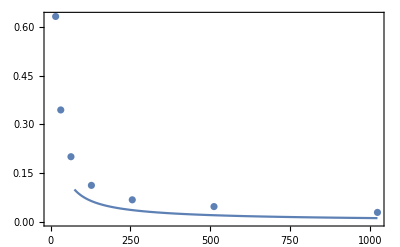

```mathematica
Show[ListPlot[data],Plot[nlm[2x],{x,0,1024}],Frame->True]
```

```mathematica
nlm3=NonlinearModelFit[data, a^{b+c*x},{a,b,c},x]
```

FittedModel[0.979992^(7.37256+1.15084 x)]

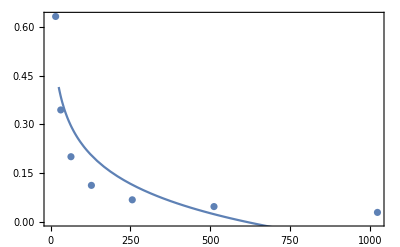

```mathematica
Show[ListPlot[data],Plot[nlm2[x],{x,0,1024}],Frame->True]
```

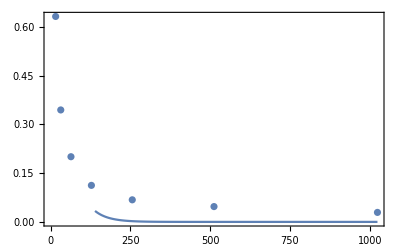

```mathematica
Show[ListPlot[data],Plot[nlm3[x],{x,0,1024}],Frame->True]
```

```mathematica
finalnlm = nlm + .1
Normal[nlm]
```

0.1+FittedModel[6.13146/x^0.822542]

6.13146/x^0.822542

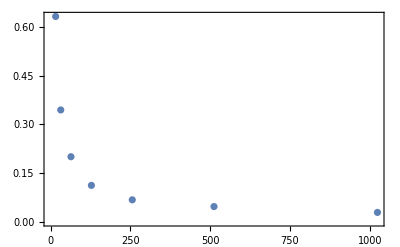

```mathematica
Show[ListPlot[data],Plot[finalnlm[x],{x,0,1024}],Frame->True]
```

```mathematica
finalnlm = 6.131462572527666/x^0.8225419740981006 + 0.1
```

0.1+6.13146/x^0.822542

finalnlm

WolframAlphaQueryResults

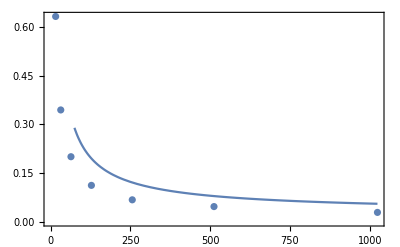

```mathematica
Show[ListPlot[data],Plot[(1.5)nlm[x]+0.025,{x,0,1024}],Frame->True]
```

```mathematica
finalnlm[100]
```

(0.1+6.13146/x^0.822542)[100]

```mathematica
FittedModel[finalnlm]
```

FittedModel[finalnlm]

```mathematica
nlm[16]+0.1
```

0.726794

```mathematica
data
```

{{16,0.631512},{32,0.344124},{64,0.200356},{128,0.112299},{256,0.067883},{512,0.047099},{1024,0.029178}}

```mathematica
0.543776
```

```mathematica
data  = {{16,0.543776},{32,0.36075},{64,0.210741},{128,0.098394},{256,0.051644},{512,0.02648},{1024,0.014001}}
```

{{16,0.543776},{32,0.36075},{64,0.210741},{128,0.098394},{256,0.051644},{512,0.02648},{1024,0.014001}}

```mathematica
nlm=NonlinearModelFit[data, a^{b+c*Log[x]},{a,b,c},x]
```

FittedModel[4.53261/x^0.754872]

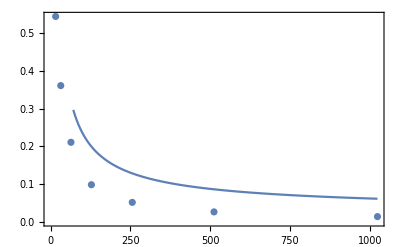

```mathematica
Show[ListPlot[data],Plot[(1.5)nlm[x]+0.025,{x,0,1024}],Frame->True]
```

```mathematica
nlm[16]
```

0.558975

```mathematica
nlm[16]+0.025
```

0.583975

```mathematica
nlm[16]*1.5+0.025
```

0.863462

```mathematica
Normal[nlm]
```

4.53261/x^0.754872

```mathematica
L2 = {{16,0.695356},{32, 0.478966},{64, 0.352937},{128, 0.240012},{256, 0.184145},{512, 0.130891},{1024, 0.082371}}
```

{{16,0.695356},{32,0.478966},{64,0.352937},{128,0.240012},{256,0.184145},{512,0.130891},{1024,0.082371}}

```mathematica
nlm2=NonlinearModelFit[L2, a^{b+c*Log[x]},{a,b,c},x]
```

FittedModel[2.71748/x^0.49428]

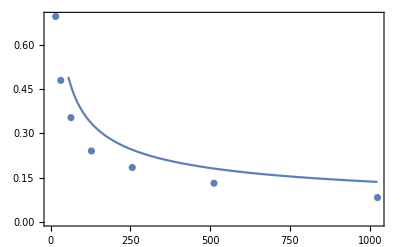

```mathematica
Show[ListPlot[L2],Plot[1.25*nlm2[x] + 0.025,{x,0,1024}],Frame->True]
```

```mathematica
1.25*nlm[16]+0.025
```

0.723719

```mathematica
L3 = {{16,0.82371},{32, 0.727282},{64, 0.533838},{128, 0.43611},{256, 0.356399},{512, 0.25657},{1024, 0.210055}}
```

{{16,0.82371},{32,0.727282},{64,0.533838},{128,0.43611},{256,0.356399},{512,0.25657},{1024,0.210055}}

```mathematica
nlm3=NonlinearModelFit[L3, a^{b+c*Log[x]},{a,b,c},x]
```

FittedModel[2.10019/x^0.325292]

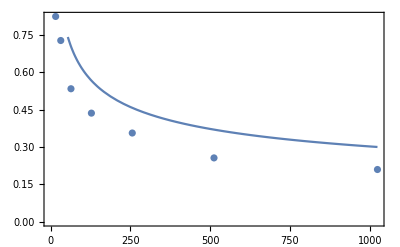

```mathematica
Show[ListPlot[L3],Plot[1.25*nlm3[x] + 0.025,{x,0,1024}],Frame->True]
```

```mathematica
L4 = {{16,0.886194},{32, 0.736967},{64, 0.680934},{128, 0.59279},{256,0.465153},{512, 0.384114},{1024, 0.311332}}
```

{{16,0.886194},{32,0.736967},{64,0.680934},{128,0.59279},{256,0.465153},{512,0.384114},{1024,0.311332}}

```mathematica
nlm4=NonlinearModelFit[L4, a^{b+c*Log[x]},{a,b,c},x]
```

FittedModel[1.71096/x^0.233472]

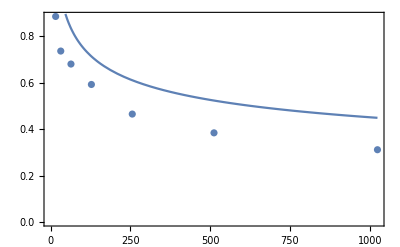

```mathematica
Show[ListPlot[L4],Plot[1.25*nlm4[x]+0.025,{x,0,1024}],Frame->True]
```